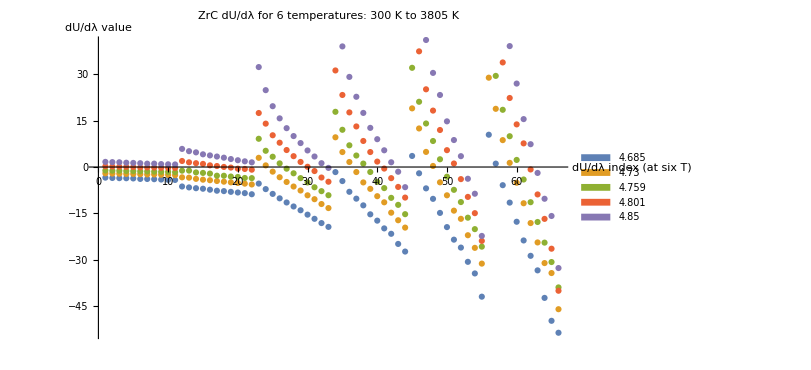

```mathematica
(*TI5 *)
(*look at fitting with Gasussian process, Pade, power series*)
(*Integrate with Gaussian quadrature and normal quadrature*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
filesEinsteinPot={"T_dudl_meam_4685","T_dudl_meam_4730","T_dudl_meam_4759","T_dudl_meam_4801","T_dudl_meam_4850"};
TdUdL=Table[ReadList[filesEinsteinPot[[i]],{Number, Number}],{i,1,5}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols={4.685,4.730,4.759,4.801,4.850};
ListPlot[Table[Transpose[TdUdL[[i]]][[2]],{i,1,5}],PlotLabel->"ZrC dU/dλ for 6 temperatures: 300 K to 3805 K",AxesLabel->{"dU/dλ index \n(at six T)","dU/dλ value"},ImageSize->600,PlotLegends->SwatchLegend[vols]]
```

```mathematica
(*Test with 4.685 dudl at 3805*)
testdudl=Table[Table[Transpose[{lambda,Partition[Transpose[TdUdL[[vol]]][[2]],11][[temps]]}],{temps,1,6}],{vol,1,5}];
```

```mathematica
testdudl;
```

```mathematica
Table[Table[NIntegrate[Interpolation[testdudl[[vol]][[temp]],x],{x,0,1}],{vol,1,5}],{temp,1,6}]
Table[Table[NIntegrate[Evaluate@Fit[testdudl[[vol]][[temp]],{1,x},x],{x,0,1}],{vol,1,5}],{temp,1,6}]
Table[Table[NIntegrate[Evaluate@Fit[testdudl[[vol]][[temp]],{1,x,x^2,x^3,x^4},x],{x,0,1}],{vol,1,5}],{temp,1,6}]
```

{{-3.81271,-2.32319,-1.37769,-0.076318,1.23441},{-7.54768,-4.48073,-2.47265,0.386097,3.43723},{-12.6874,-5.98305,-1.60999,4.43559,11.5908},{-14.868,-6.53067,-1.03384,6.8781,15.7602},{-18.677,-8.13396,-0.953528,8.43489,19.6635},{-23.4326,-10.3236,-2.59853,8.90141,22.768}}

{{-3.81086,-2.32511,-1.37765,-0.0747147,1.23635},{-7.54971,-4.48553,-2.46836,0.401138,3.46697},{-12.6504,-5.89282,-1.42953,4.62654,12.0568},{-14.8271,-6.36335,-0.809673,7.26492,16.4483},{-18.7683,-7.97361,-0.533527,8.87368,20.4628},{-23.188,-10.2626,-2.05408,9.47988,24.2708}}

{{-3.81143,-2.32337,-1.37785,-0.0762672,1.23554},{-7.54809,-4.48527,-2.47588,0.385152,3.44112},{-12.686,-5.97792,-1.59493,4.43411,11.6014},{-14.8639,-6.51571,-1.06442,6.89367,15.7243},{-18.7054,-8.18144,-0.948908,8.35227,19.5159},{-23.3822,-10.4777,-2.61856,8.841,22.7188}}

```mathematica
twoFit=Table[Table[Fit[testdudl[[vol]][[temp]],{1,x,x^2},x],{temp,1,6}],{vol,1,5}];
quadFit=Table[Table[Fit[testdudl[[vol]][[temp]],{1,x,x^2,x^3,x^4},x],{temp,1,6}],{vol,1,5}];
```

```mathematica
bound1=0;bound2=1; 
mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{x,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&x∈Interval[{0,1}],x,Reals]//N
```

```mathematica
Table[Table[mvtSolver[quadFit[[vol]][[temp]]],{vol,1,5}],{temp,1,6}]//TableForm
```

x→{0.526777} | x→{0.512834} | x→{0.506657} | x→{0.476992} | x→{0.489351}
x→{0.480566} | x→{0.477321} | x→{0.459031} | x→{0.477058} | x→{0.484046}
x→{0.496349} | x→{0.478999} | x→{0.471391} | x→{0.450963} | x→{0.437572}
x→{0.49131} | x→{0.479579} | x→{0.47172} | x→{0.444277} | x→{0.43044}
x→{0.486876} | x→{0.472735} | x→{0.464804} | x→{0.452548} | x→{0.429183}
x→{0.510715} | x→{0.471979} | x→{0.471657} | x→{0.466716} | x→{0.428318}

x→{0.498928}
x→{0.474379}
x→{0.469446}
x→{0.456894}
x→{0.431042}

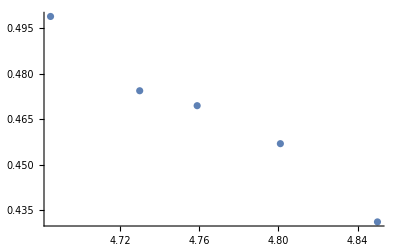

```mathematica
mvtVol=Table[Solve[Total[Table[(quadFit[[vol]][[temp]]-Integrate[quadFit[[vol]][[temp]],{x,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2}),{temp,1,6}]]==0&&x∈Interval[{0,1}],x,Reals],{vol,1,5}];
mvtVol//TableForm
ListPlot@Transpose@{vols,Flatten@Table[mvtVol[[i]][[1]][[1]][[2]],{i,1,5}]}
```

```mathematica
data=Transpose@{vols,Flatten@Table[mvtVol[[i]][[1]][[1]][[2]],{i,1,5}]}
Flatten[{#1->#2}&@@@data]
```

{{4.685,0.498928},{4.73,0.474379},{4.759,0.469446},{4.801,0.456894},{4.85,0.431042}}

{4.685→0.498928,4.73→0.474379,4.759→0.469446,4.801→0.456894,4.85→0.431042}

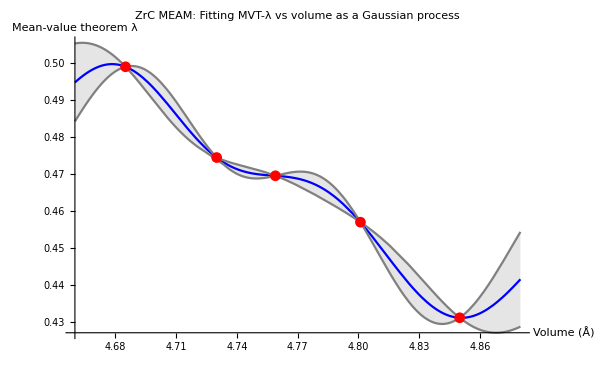

```mathematica
p=Predict[Flatten[{#1->#2}&@@@data],Method->"GaussianProcess"];
Show[Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,4.66,4.88},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->Placed[{"Gasussian prediction","1-σ confidence interval"},{0.85,0.8}]],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->Placed[{"ZrC dU/dλ at five volumes"},{0.85,0.8}]],AxesLabel->{"Volume (Å)","Mean-value\n theorem λ"},ImageSize->600,PlotLabel->"ZrC MEAM: Fitting MVT-λ vs volume as a Gaussian process"]
```

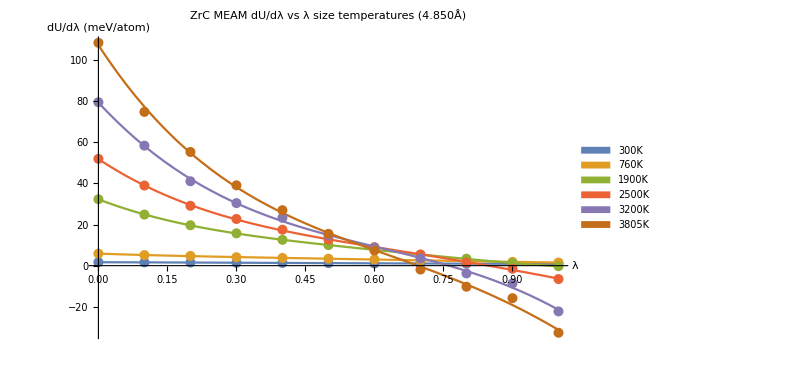

```mathematica
plotoptions5={AxesLabel->{"λ","dU/dλ (meV/atom)"},ImageSize->600,PlotLabel->"ZrC MEAM dU/dλ vs λ size temperatures (4.850Å)"};
Show[Plot[Evaluate@quadFit[[5]],{x,0,1},PlotRange->All,Evaluate@plotoptions5,PlotLegends->Placed[SwatchLegend[{"300K","760K","1900K","2500K","3200K","3805K"}],{0.9,0.5}]],ListPlot[testdudl[[5]],PlotStyle->PointSize[0.012]]]
```

{{{300,0.489351},{760,0.484046},{1900,0.437572},{2500,0.43044},{3200,0.429183},{3805,0.428318}}}

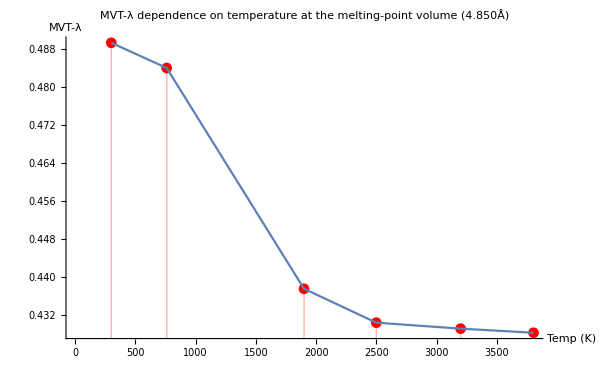

```mathematica
fourData=Table[Transpose[{temps,Flatten[x/.Table[mvtSolver[quadFit[[vol]][[temp]]],{temp,1,6}]]}],{vol,5,5}]
plotoptions4={AxesLabel->{"Temp (K)","MVT-λ"},ImageSize->600,PlotLabel->"MVT-λ dependence on temperature at the melting-point volume (4.850Å)"};
Show[ListPlot[fourData,PlotStyle->Red,Filling->Axis,Evaluate@plotoptions4],ListPlot[fourData,Joined->True]]
```

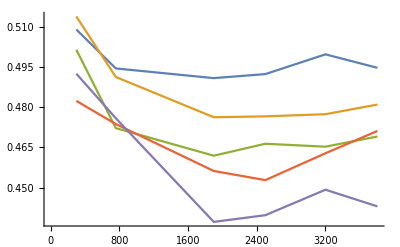

```mathematica
ListPlot[Table[Transpose[{temps,Flatten[x/.Table[mvtSolver[twoFit[[vol]][[temp]]],{temp,1,6}]]}],{vol,1,5}],Joined->True]
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];MVTintAll=Transpose@ReadList["MVT_intall",{Number, Number,Number,Number,Number}];
FahData=Integrate[Table[Table[Fit[Partition[TdUdL[[vol]],11][[temp]],{1,x,x^2,x^3,x^4},x],{temp,1,6}],{vol,1,5}],{x,0,1}];
```

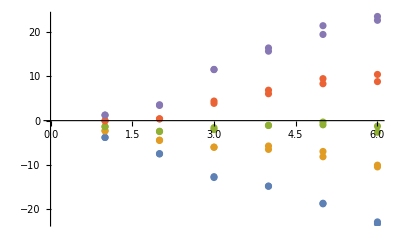

```mathematica
Show[ListPlot[MVTintAll],ListPlot[FahData]]
```

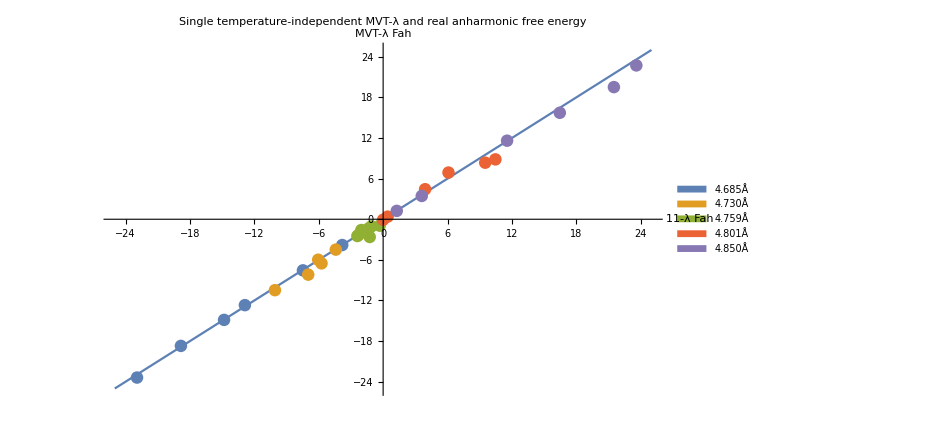

```mathematica
plotoptions5={AxesLabel->{"11-λ Fah","MVT-λ Fah"},ImageSize->700,PlotLabel->"Single temperature-independent MVT-λ and real anharmonic free energy",ImageSize->600};
Show[Plot[x,{x,-25,25},Evaluate@plotoptions5],ListPlot[Partition[Transpose@{Flatten@MVTintAll,Flatten@FahData},6],PlotLegends->Placed[SwatchLegend[{"4.685Å","4.730Å","4.759Å","4.801Å","4.850Å"}],{0.90,0.2}]]]
```